```mathematica
Solve[x^2+3x==5,x]
```

{{x→1/2 (-3-√29)},{x→1/2 (-3+√29)}}

```mathematica
NSolve[x^2+3x==5,x]
```

{{x→-4.19258},{x→1.19258}}

# Дифференциальные уравнения

```mathematica
Sin'[x]
```

Cos[x]

```mathematica
Sin''[x]
```

-Sin[x]

'  ≠ `
'' ≠ "

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
NIntegrate[Sin[x],{x,0,1}]
```

0.459698

```mathematica
∫_1^3 Sin[x]ⅆx
```

2 Sin[1] Sin[2]

```mathematica
sol=DSolve[x''[t]==-x[t],x,t]
```

{{x→Function[{t},C[1] Cos[t]+C[2] Sin[t]]}}

```mathematica
x/.sol
```

{Function[{t},C[1] Cos[t]+C[2] Sin[t]]}

```mathematica
x[t]/.sol⟦1⟧
```

C[1] Cos[t]+C[2] Sin[t]

```mathematica
DSolve[x''[t]==-x'[t]-Sin[x[t]],x,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[x''[t]==-Sin[x[t]]-x'[t],x,t]

```mathematica
sol=NDSolve[{
x''[t]==-x'[t]-Sin[x[t]],
x'[0]==1,x[0]==0
},
x,{t,0,10}]⟦1⟧
```

{x→InterpolatingFunction[…]}

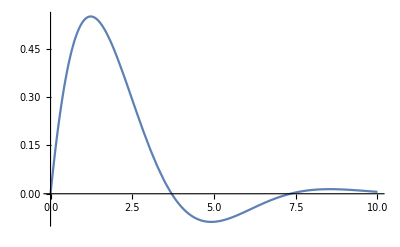

```mathematica
Plot[x[t]/.sol,{t,0,10}]
```

```mathematica
sol⟦1,2⟧
```

InterpolatingFunction[…]

```mathematica
sol⟦1,2⟧//FullForm
```

InterpolatingFunction[List[List[0.,10.]],List[5,7,2,List[95],List[4],0,0,0,0,Automatic,List[],List[],False],List[List[0.,0.000128815,0.00025763,0.00532777,0.0103979,0.015468,0.0297266,0.0439851,0.0582436,0.0725022,0.101019,0.129536,0.158053,0.18657,0.215088,0.261455,0.307822,0.354189,0.400556,0.446923,0.49329,0.555265,0.61724,0.679215,0.74119,0.803165,0.86514,0.927115,1.00706,1.08701,1.16696,1.24691,1.32686,1.40681,1.48676,1.59445,1.70214,1.80982,1.91751,2.0252,2.13289,2.24057,2.34826,2.45595,2.56364,2.69852,2.83341,2.9683,3.10319,3.23807,3.37296,3.50785,3.64273,3.77762,3.91251,4.0474,4.18228,4.31717,4.46704,4.61691,4.76677,4.91664,5.06651,5.21637,5.36624,5.51611,5.68341,5.8507,6.018,6.18529,6.35259,6.51989,6.68718,6.85448,7.02178,7.18907,7.35637,7.51099,7.66562,7.82024,7.97486,8.12949,8.28411,8.43874,8.59327,8.74781,8.90234,9.05688,9.21141,9.36595,9.52048,9.675,9.82951,9.91476,10.]],List[Developer`PackedArrayForm,List[0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285],List[0.,1.,-1.,0.000128798,0.999871,-1.,0.00025758,0.999742,-1.,0.00531356,0.994672,-0.999986,0.0103438,0.989602,-0.999946,0.0153484,0.984533,-0.99988,0.0292848,0.970278,-0.999558,0.0430179,0.956029,-0.999034,0.056548,0.941789,-0.998307,0.069875,0.927561,-0.997379,0.0959211,0.899152,-0.994926,0.121158,0.870824,-0.991686,0.145589,0.842599,-0.987674,0.169216,0.8145,-0.98291,0.192044,0.786547,-0.977413,0.227467,0.741462,-0.966973,0.260812,0.696903,-0.954767,0.292103,0.652948,-0.940915,0.321373,0.609671,-0.92554,0.348652,0.56714,-0.908772,0.373979,0.525416,-0.890738,0.404847,0.471004,-0.864882,0.432394,0.41825,-0.837295,0.456725,0.367252,-0.808263,0.477953,0.31809,-0.778052,0.496192,0.270831,-0.746911,0.511562,0.225525,-0.715065,0.524187,0.182209,-0.682718,0.536617,0.12931,-0.640541,0.544953,0.0797922,-0.59817,0.549466,0.0336602,-0.555892,0.550425,-0.00910355,-0.513946,0.548099,-0.0485338,-0.472532,0.542752,-0.0846798,-0.431815,0.534645,-0.117603,-0.391933,0.51981,-0.156982,-0.339733,0.501033,-0.190843,-0.289489,0.478897,-0.219408,-0.241393,0.45396,-0.242916,-0.195612,0.426752,-0.261626,-0.15229,0.397775,-0.275808,-0.111559,0.367502,-0.28575,-0.0735353,0.336373,-0.291747,-0.0383189,0.304798,-0.294107,-0.00599351,0.27315,-0.293144,0.0233783,0.233923,-0.287741,0.0559454,0.195707,-0.278263,0.0838025,0.159009,-0.265343,0.107002,0.124252,-0.2496,0.125668,0.0917734,-0.231636,0.139991,0.0618362,-0.212018,0.150222,0.0346265,-0.19128,0.156661,0.0102619,-0.16991,0.159649,-0.0112026,-0.14835,0.159552,-0.0297682,-0.126989,0.156753,-0.0454853,-0.106166,0.151636,-0.0584463,-0.0861684,0.144581,-0.0687792,-0.0672322,0.135957,-0.0773682,-0.047665,0.124956,-0.0831527,-0.0298318,0.112889,-0.086403,-0.0138616,0.100157,-0.0874043,0.000173501,0.0871195,-0.0864488,0.0122516,0.0740896,-0.0838288,0.0223946,0.0613361,-0.0798302,0.0306612,0.0490842,-0.0747279,0.037141,0.0375173,-0.0680462,0.0424043,0.0255895,-0.0606456,0.0457689,0.0148396,-0.0528267,0.0474405,0.00536166,-0.0448547,0.0476365,-0.00279686,-0.0369578,0.0465787,-0.0096293,-0.0293274,0.044487,-0.0151638,-0.0221185,0.0415742,-0.0194575,-0.0154515,0.0380415,-0.0225905,-0.00941431,0.0340749,-0.0246607,-0.00406507,0.0298433,-0.0257782,0.000564636,0.0254963,-0.0260609,0.00419637,0.0214885,-0.0256848,0.00721503,0.0175798,-0.0247947,0.00964173,0.0138424,-0.023484,0.0115076,0.0103345,-0.0218418,0.0128518,0.00710062,-0.0199521,0.0137193,0.00417309,-0.0178919,0.0141592,0.00157273,-0.0157314,0.0142231,-0.000688669,-0.013534,0.0139638,-0.00261106,-0.0113523,0.0134333,-0.00420053,-0.00923235,0.0126821,-0.00546966,-0.00721207,0.0117584,-0.00643628,-0.00532181,0.0107073,-0.00712237,-0.00358468,0.00957021,-0.00755295,-0.00201712,0.0083848,-0.00775507,-0.000629629,0.00718398,-0.00775704,0.000573126,0.00652555,-0.00768289,0.00115739,0.00587549,-0.00756131,0.00168585]],List[Automatic]]

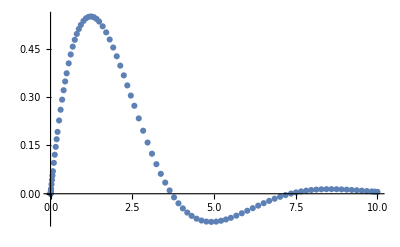

```mathematica
ListPlot[{sol⟦1,2,3,1⟧,sol⟦1,2,4,3,sol⟦1,2,4,2,;;-2⟧+1⟧}ᵀ]
```